```mathematica
n=4;
data=Import[NotebookDirectory[]<>"common_value_full_test.csv"];
data=Partition[data,3*n+1];
profits=data[[All,-1]];
data=data[[All,1;;-2]];
```

```mathematica
plots=Table[
points=Table[
mids=data[[i,1+3j]];
unc=data[[i,2+3j]];
bf=data[[i,3+3j]];
bf=Partition[bf,Length[unc]];
midMesh=Table[mids,Length[unc]];
uncMesh=Transpose[Table[unc,Length[mids]]];
points=Flatten[MapThread[List,{midMesh,uncMesh,bf},2],1];
points=Select[points,#[[2]]≤1000&];
points=Select[points,#[[1]]≥(500-#[[2]]/2)&];
points=Select[points,#[[1]]≤(9500+#[[2]]/2)&];
slice=Select[points,#[[2]]==500&];
slice2=Select[points,#[[1]]==5000&];
{points,slice,slice2}
,{j,0,3}
];
{ListLinePlot[Thread[{#[[All,1]],#[[All,3]]-#[[All,1]]}]&/@points[[All,2]],PlotRange->{-500,0}],(*ListPlot3D[points[[1]],AxesLabel->{"Midpoint","Uncertainty","Bid"}],*)
{},
{},
(*ListContourPlot[points,FrameLabel->{"Midpoint","Uncertainty"},PlotRangePadding->0],*)
ListLinePlot[Thread[{#[[All,2]],#[[All,3]]-5000}]&/@points[[All,3]],PlotRange->{-500,500}]}
,{i,1,Length[data]}
];
```

Partition::ilsmp: Single or list of positive machine-sized integers expected at position 2 of Partition[{907.439,2337.32,2373.47,2509.59,4195.53,5891.67,4215.52,320.748,953.731,2406.97,3245.97,3306.03,4135.89,2766.02,2849.36,3038.65,5210.04,5876.41,4727.36,1198.29,1538.11,«9»,4375.07,1488.26,3674.49,3951.8,4546.5,5960.69,5812.24,4955.48,5271.83,5340.7,5519.93,6489.77,5460.2,2238.93,3476.33,8050.23,8171.09,8639.06,4918.94,1070.18,«3671»},0].

MapThread::mptd: Object {} at position {2, 1} in MapThread[List,{{},{«1»},Partition[{907.439,2337.32,2373.47,2509.59,4195.53,5891.67,4215.52,320.748,953.731,2406.97,3245.97,3306.03,4135.89,2766.02,2849.36,3038.65,5210.04,5876.41,4727.36,1198.29,«12»,3674.49,3951.8,4546.5,5960.69,5812.24,4955.48,5271.83,5340.7,5519.93,6489.77,5460.2,2238.93,3476.33,8050.23,8171.09,8639.06,4918.94,1070.18,«3671»},0]},2] has only 1 of required 2 dimensions.

Part::partd: Part specification List⟦2⟧ is longer than depth of object.

Part::partd: Part specification 2⟦2⟧ is longer than depth of object.

MapThread::argt: MapThread called with 0 arguments; 2 or 3 arguments are expected.

General::stop: Further output of MapThread::argt will be suppressed during this calculation.

Partition::ilsmp: Single or list of positive machine-sized integers expected at position 2 of Partition[{183.155,1161,2172.17,2708.61,2739.41,5667.73,3896.42,1599.74,2109.07,2717.96,5897.42,6034.02,3848.17,220.768,1725.03,4282.29,5233.82,6281.24,4052.36,1954.73,2292.88,«9»,4424.4,2552.86,2960.72,3463.68,4378.54,4504.33,3018.27,1081.88,2060.06,2249.68,3012.59,3199.65,3588.77,1099.53,2417.47,3112.01,6451.41,6764.11,4662.68,1319.6,«3671»},0].

MapThread::mptd: Object {} at position {2, 1} in MapThread[List,{{},{{«1»},«49»,«11»},Partition[{183.155,1161,2172.17,2708.61,2739.41,5667.73,3896.42,1599.74,2109.07,2717.96,5897.42,6034.02,3848.17,220.768,1725.03,4282.29,5233.82,6281.24,4052.36,«13»,2960.72,3463.68,4378.54,4504.33,3018.27,1081.88,2060.06,2249.68,3012.59,3199.65,3588.77,1099.53,2417.47,3112.01,6451.41,6764.11,4662.68,1319.6,«3671»},0]},2] has only 1 of required 2 dimensions.

Part::partd: Part specification List⟦2⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

Partition::ilsmp: Single or list of positive machine-sized integers expected at position 2 of Partition[{829.505,1187.66,1325.69,2632.34,3262.62,5077,3535.06,1687.89,1858.35,2814.22,3593.82,7237.54,5139.4,1137.5,1515.73,2615.8,2730.49,5102.99,3441.65,1008.74,1166.38,«9»,6021.76,4216.1,5433.16,6329.55,6426.31,8117.87,6395.76,4612.08,6513.49,6955.8,7551.28,8451.95,4616.17,721.777,1089.52,2211.62,4984.78,6523.89,3519.55,2779.47,«3671»},0].

General::stop: Further output of Partition::ilsmp will be suppressed during this calculation.

MapThread::mptd: Object {} at position {2, 1} in MapThread[List,{{},{«1»},Partition[{829.505,1187.66,1325.69,2632.34,3262.62,5077,3535.06,1687.89,1858.35,2814.22,3593.82,7237.54,5139.4,1137.5,1515.73,2615.8,2730.49,5102.99,3441.65,1008.74,«11»,4216.1,5433.16,6329.55,6426.31,8117.87,6395.76,4612.08,6513.49,6955.8,7551.28,8451.95,4616.17,721.777,1089.52,2211.62,4984.78,6523.89,3519.55,2779.47,«3671»},0]},2] has only 1 of required 2 dimensions.

General::stop: Further output of MapThread::mptd will be suppressed during this calculation.

```mathematica
Manipulate[plots[[i,2]],{i,1,Length[plots],1}]
```

Part::partd: Part specification plots⟦100,2⟧ is longer than depth of object.

```mathematica
Manipulate[plots[[i,1]],{i,1,Length[plots],1}]
```

Part::partd: Part specification plots⟦100,1⟧ is longer than depth of object.

```mathematica
Manipulate[plots[[i,3]],{i,1,Length[plots],1}]
```

Part::partd: Part specification plots⟦100,3⟧ is longer than depth of object.

```mathematica
Manipulate[plots[[i,4]],{i,1,Length[plots],1}]
```

Part::partd: Part specification plots⟦100,4⟧ is longer than depth of object.

```mathematica
type="max";
n=4;
data=Import[NotebookDirectory[]<>"biddingga3/biddingga/output/fpa2d_"<>ToString[n]<>"p_"<>type<>"_10_100_60_5k.csv"];
data=Partition[data,4*n+3];
value=data[[All,-3]];
revenue=data[[All,-2]];
profits=data[[All,-1]];
data=data[[All,1;;-4]];
```

```mathematica
Max[data[[-1,3]]]
```

0.681248

```mathematica
means=Mean[data[[-3;;-1,4]]];
```

```mathematica
res=Partition[data[[-1,3]],Length[data[[-1,1]]]];
```

```mathematica
res=(res[[;;-2,;;-2]]+res[[;;-2,2;;]]+res[[2;;,;;-2]]+res[[2;;,2;;]])/4;
```

```mathematica
ListPlot3D[res]
```

-Graphics3D-

```mathematica
Transpose[{data[[1,1]],data[[1,2]],#}]Partition[data[[1,3]],Length[data[[-1,1]]]]
```

```mathematica
zs=Partition[data[[-1,3]],Length[data[[1,2]]]];
```

```mathematica
Flatten[MapThread[List,{xmesh,ymesh,zs},2],1]
```

{{0,0,0.0100269},{0,0.0166667,0.0116214},{0,0.0333333,0.0259774},{0,0.05,0.037818},{0,0.0666667,0.0464494},{0,0.0833333,0.0638601},{0,0.1,0.0743231},{0,0.116667,0.0937817},{0,0.133333,0.0991129},{0,0.15,0.108993},{0,0.166667,0.129123},{0,0.183333,0.136664},{0,0.2,0.148239},{0,0.216667,0.163457},{0,0.233333,0.17522},{0,0.25,0.188181},{0,0.266667,0.200266},3687,{1,0.733333,0.55089},{1,0.75,0.563791},{1,0.766667,0.575287},{1,0.783333,0.589301},{1,0.8,0.595685},{1,0.816667,0.61424},{1,0.833333,0.62485},{1,0.85,0.637888},{1,0.866667,0.650457},{1,0.883333,0.663},{1,0.9,0.671858},{1,0.916667,0.686156},{1,0.933333,0.698673},{1,0.95,0.711784},{1,0.966667,0.722295},{1,0.983333,0.738622},{1,1,0.74906}}
 |  |  |  |

```mathematica
data[[-1,3]]
```

```mathematica
ConstantArray[data[[1,1]],
```

```mathematica
id=0;
xmesh=ConstantArray[data[[1,1]],Length[data[[1,2]]]];
ymesh=Transpose[ConstantArray[data[[1,2]],Length[data[[1,1]]]]];
cplotsx=Table[
zs=Partition[data[[i,4*id+3]],Length[data[[1,1]]]];
zs=Flatten[MapThread[List,{xmesh,ymesh,zs},2],1];
ListContourPlot[zs,FrameLabel->{"A","B"},ImageSize->Medium,PlotLabel->"Bid A",PlotRangePadding->0,Contours->Table[i/10.,{i,1,10}]]
,{i,1,Length[data]}
];
cplotsy=Table[
zs=Partition[data[[i,4*id+4]],Length[data[[1,1]]]];
zs=Flatten[MapThread[List,{xmesh,ymesh,zs},2],1];
ListContourPlot[zs,FrameLabel->{"A","B"},ImageSize->Medium,PlotLabel->"Bid B",PlotRangePadding->0,Contours->Table[i/10.,{i,1,10}],
PlotLegends->BarLegend[{Automatic,{0,1}}]]
,{i,1,Length[data]}
];
```

```mathematica
Export[NotebookDirectory[]<>"d0_4.gif",Table[Row[{cplotsx[[i]],cplotsy[[i]]}],{i,1,Length[cplotsx]}],ImageResolution->100];
```

```mathematica
id=7;
xmesh=ConstantArray[data[[1,1]],Length[data[[1,2]]]];
ymesh=Transpose[ConstantArray[data[[1,2]],Length[data[[1,1]]]]];
lx=Table[
zs=Partition[data[[i,4*id+3]],Length[data[[1,1]]]];
zs=Flatten[MapThread[List,{xmesh,ymesh,zs},2],1];
ListPlot3D[zs,AxesLabel->{"A","B","Bid A"},PlotRange->{0,1}, ImageSize->Large,ViewPoint->{-2.1,-2.1,1.3}]
,{i,1,Length[data]}
];
ly=Table[
zs=Partition[data[[i,4*id+4]],Length[data[[1,1]]]];
zs=Flatten[MapThread[List,{xmesh,ymesh,zs},2],1];
ListPlot3D[zs,AxesLabel->{"A","B","Bid B"},PlotRange->{0,1}, ImageSize->Large,ViewPoint->{-2.1,-2.1,1.3}]
,{i,1,Length[data]}
];
```

```mathematica
Length[data]
```

100

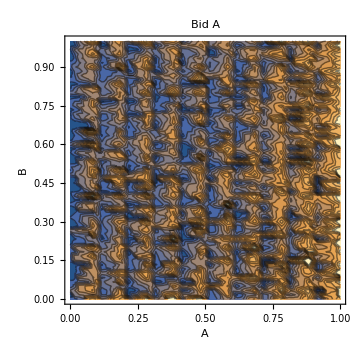

```mathematica
cplotsx[[1]]
```

```mathematica
Manipulate[
Grid[{{lx[[i]],ly[[i]]},{cplotsx[[i]],cplotsy[[i]]}}]
,{i,1,Length[lx],1}
]
```

```mathematica
Table[
Export[NotebookDirectory[]<>"text/chapter_3/figures/4p_max_"<>ToString[i*50]<>".jpg",Grid[{{lx[[i]],ly[[i]]},{cplotsx[[i]],cplotsy[[i]]}}], ImageResolution->150]
,{i,{1,10,100}}
]
```

{/home/kajames/Dropbox/Dissertation/text/chapter_3/figures/4p_max_50.jpg,/home/kajames/Dropbox/Dissertation/text/chapter_3/figures/4p_max_500.jpg,/home/kajames/Dropbox/Dissertation/text/chapter_3/figures/4p_max_5000.jpg}

```mathematica
Export[NotebookDirectory[]<>"4p_d100_3d.gif",Table[Grid[{{lx[[i]],ly[[i]]},{cplotsx[[i]],cplotsy[[i]]}}],{i,1,100}], ImageResolution->50]
```

/home/kajames/Dropbox/Dissertation/4p_d100_3d.gif

```mathematica
ListPlot3D[Partition[data[[-1,4]],Length[data[[-1,1]]]],PlotRange->{0,1},AxesLabel->{"A","B","Bid B"},ImageSize->Large]
```

-Graphics3D-

```mathematica
D12D[xs_,ys_,points_,opt_]:=Module[{res,areas},
res=(points-opt)^2;
res=(res[[;;-2,;;-2]]+res[[2;;,;;-2]]+res[[;;-2,2;;]]+res[[2;;,2;;]])/4;
areas=Outer[Times,(Rest[xs]-Most[xs]),(Rest[ys]-Most[ys])];
(1/((Last[xs]-First[xs])*(Last[ys]-First[ys])))*Sqrt[Total[res*areas,Infinity]]
];
D22D[xs_,ys_,points_,opt_]:=Module[{res,areas},
res=(points-opt);
res=(res[[;;-2,;;-2]]+res[[2;;,;;-2]]+res[[;;-2,2;;]]+res[[2;;,2;;]])/4;
areas=Outer[Times,(Rest[xs]-Most[xs]),(Rest[ys]-Most[ys])];
(1/((Last[xs]-First[xs])*(Last[ys]-First[ys])))*Total[res*areas,Infinity]
]
```

```mathematica
xs=data[[i,1]];
ys=data[[i,2]];
d1As=Table[
zs=Partition[data[[i,4*id+3]],Length[data[[1,1]]]];
D12D[xs,ys,zs,3/4*xmesh]
,{i,1,100}
];
d1As=Transpose[{Range[50,5000,50],d1As}];
d1Bs=Table[
zs=Partition[data[[i,4*id+4]],Length[data[[1,1]]]];
D12D[xs,ys,zs,3/4*ymesh]
,{i,1,100}
];
d1Bs=Transpose[{Range[50,5000,50],d1Bs}];
d2As=Table[
zs=Partition[data[[i,4*id+3]],Length[data[[1,1]]]];
D22D[xs,ys,zs,3/4*xmesh]
,{i,1,100}
];
d2As=Transpose[{Range[50,5000,50],d2As}];
d2Bs=Table[
zs=Partition[data[[i,4*id+4]],Length[data[[1,1]]]];
D22D[xs,ys,zs,3/4*ymesh]
,{i,1,100}
];
d2Bs=Transpose[{Range[50,5000,50],d2Bs}];
```

```mathematica
d1As
```

{{50,0.243225},{100,0.195251},{150,0.161884},{200,0.134272},{250,0.113565},{300,0.0976025},{350,0.0838591},{400,0.0728253},{450,0.063771},{500,0.055397},{550,0.0492506},{600,0.0438786},{650,0.0385052},{700,0.034761},{750,0.0313815},{800,0.0275525},{850,0.0244305},{900,0.0222035},{950,0.0192193},{1000,0.0171796},{1050,0.0154352},{1100,0.0137588},{1150,0.0127555},{1200,0.0118633},{1250,0.0111674},{1300,0.0104297},{1350,0.00925086},{1400,0.00804274},{1450,0.00735842},{1500,0.00680711},{1550,0.0064368},{1600,0.00607887},{1650,0.00551935},{1700,0.00537389},{1750,0.00513174},{1800,0.0048404},{1850,0.00467178},{1900,0.00449994},{1950,0.00436608},{2000,0.00425629},{2050,0.00416632},{2100,0.00388797},{2150,0.00371491},{2200,0.00362577},{2250,0.00340737},{2300,0.00296843},{2350,0.00278103},{2400,0.0027015},{2450,0.00261446},{2500,0.00247297},{2550,0.00240849},{2600,0.0023306},{2650,0.00227098},{2700,0.00221879},{2750,0.0021544},{2800,0.00206847},{2850,0.00202107},{2900,0.001982},{2950,0.00191099},{3000,0.0018623},{3050,0.00181358},{3100,0.00176624},{3150,0.0017171},{3200,0.00168346},{3250,0.0016365},{3300,0.00158769},{3350,0.00154582},{3400,0.00153202},{3450,0.00148899},{3500,0.00144812},{3550,0.00142256},{3600,0.00136943},{3650,0.00134193},{3700,0.00129694},{3750,0.00126709},{3800,0.00124603},{3850,0.00121403},{3900,0.00119229},{3950,0.00115776},{4000,0.00113081},{4050,0.00111123},{4100,0.00108411},{4150,0.0010786},{4200,0.00104564},{4250,0.00105455},{4300,0.00104506},{4350,0.00102798},{4400,0.00101459},{4450,0.00100465},{4500,0.000996337},{4550,0.000982593},{4600,0.000971878},{4650,0.000946888},{4700,0.000927092},{4750,0.000920789},{4800,0.000917517},{4850,0.000909591},{4900,0.00089789},{4950,0.000886773},{5000,0.000882953}}

```mathematica
Total@Table[((i+1)/(i+2))*(Binomial[3,i]*(1/2)^(3-i)*(1/2)^i),{i,1,3}]
```

101/160

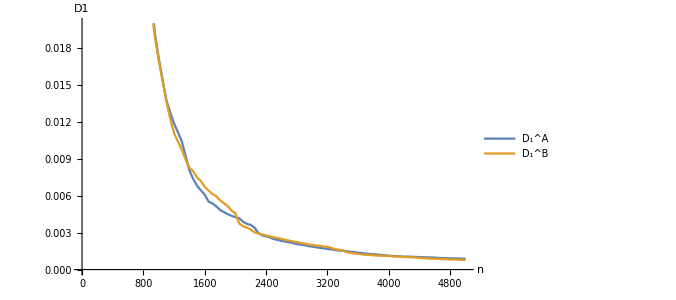

```mathematica
d1Plot=ListLinePlot[{d1As,d1Bs},PlotRange->{0,0.02},AxesLabel->{"n","D1"},LabelStyle->14,AspectRatio->0.6, ImageSize->{500,300},PlotLegends->Placed[{"D_1^A","D_1^B"},{Right,Top}]]
```

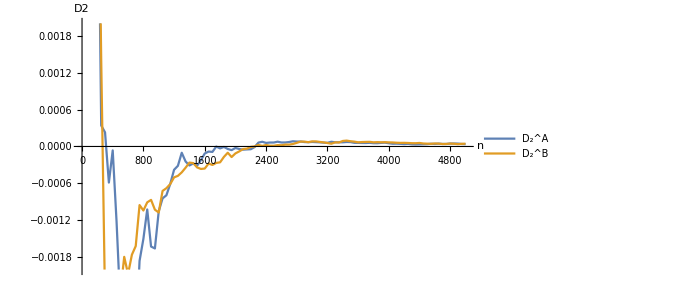

```mathematica
d2Plot=ListLinePlot[{d2As,d2Bs},PlotRange->{-0.002,0.002},AxesLabel->{"n","D2"},LabelStyle->14,AspectRatio->0.6, ImageSize->{500,300},PlotLegends->Placed[{"D_2^A","D_2^B"},{Right,Top}]]
```

```mathematica
Export[NotebookDirectory[]<>"text/chapter_3/figures/d1.jpg",d1Plot,ImageResolution->200];
Export[NotebookDirectory[]<>"text/chapter_3/figures/d2.jpg",d2Plot,ImageResolution->200];
```

0.243225

```mathematica
data=Most[data];
```

```mathematica
profits[[-1]]
```

{0.542794,0.542472}

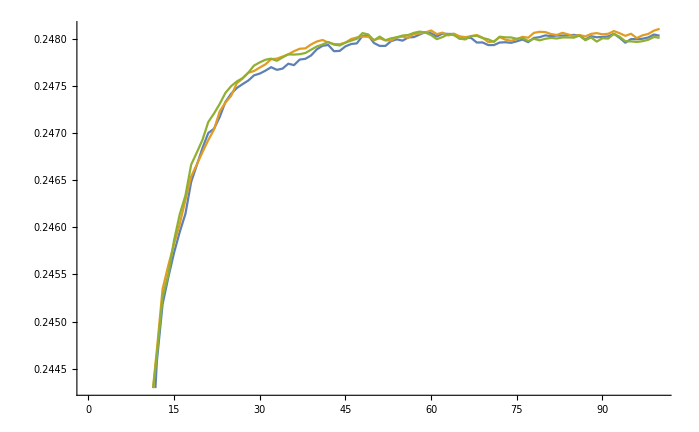

```mathematica
ListLinePlot[Transpose[profits]]
```

```mathematica
data=Most/@data;
data=Partition[data,7];
profits=data[[All,-1]];
data=data[[All,;;-2]];
data=Partition[#,2]&/@data;
data=Map[Transpose,data,{-3}];
```

```mathematica
Manipulate[
Show[Plot[x*2/3,{x,0,30},PlotRange->{0,30}],
ListLinePlot[data[[i]]],
ImageSize->Large,
Frame->{{True,False},{False,True}},
FrameTicks->{{All,None},{None,All}},
FrameLabel->{{"Relative Bid",None},{None,"Precision"}},
LabelStyle->14
],{i,1,Length[data]-100,1}
]
```

```mathematica
cplotsx2=Table[
zs=Partition[data[[i,3]],Length[data[[1,1]]]];
zs=Flatten[MapThread[List,{xmesh,ymesh,zs},2],1];
ListContourPlot[zs,FrameLabel->{"X","Y"},ImageSize->Large,PlotLabel->"Bid X",PlotRangePadding->0,Contours->Table[i/10.,{i,1,10}]]
,{i,1,Length[data]}
];
cplotsy2=Table[
zs=Partition[data[[i,4]],Length[data[[1,1]]]];
zs=Flatten[MapThread[List,{xmesh,ymesh,zs},2],1];
ListContourPlot[zs,FrameLabel->{"X","Y"},ImageSize->Large,PlotLabel->"Bid Y",PlotRangePadding->0,Contours->Table[i/10.,{i,1,10}],PlotLegends->BarLegend[{Automatic,{0,1}}]]
,{i,1,Length[data]}
];
```

```mathematica
Manipulate[Row[{cplotsx2[[i]],cplotsy2[[i]]}],{i,1,Length[cplotsx2],1}]
```

Part::partd: Part specification cplotsx2⟦100⟧ is longer than depth of object.

Part::partd: Part specification cplotsy2⟦100⟧ is longer than depth of object.

Part::partd: Part specification cplotsx2⟦100⟧ is longer than depth of object.

Part::partd: Part specification cplotsy2⟦100⟧ is longer than depth of object.

Part::partd: Part specification cplotsx2⟦100⟧ is longer than depth of object.

Part::partd: Part specification cplotsy2⟦100⟧ is longer than depth of object.

```mathematica
res=Import[NotebookDirectory[]<>"biddingga3/biddingga/sample_ga.csv"];
```

```mathematica
res=Most/@res;
```

```mathematica
xs=Range[-3,3,0.01];
ysTrue=Table[Sin[x],{x,xs}];
```

```mathematica
ySets=Table[val[[1]]+val[[2]]*xs + val[[3]]*xs^2 + val[[4]]*xs^3,{val, res}];
```

```mathematica
ySets=data[[All,All,All,2]];
```

Symbol::argx: Symbol called with 0 arguments; 1 argument is expected.

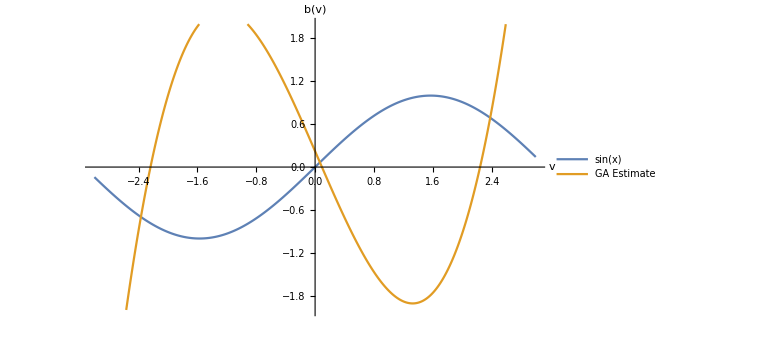
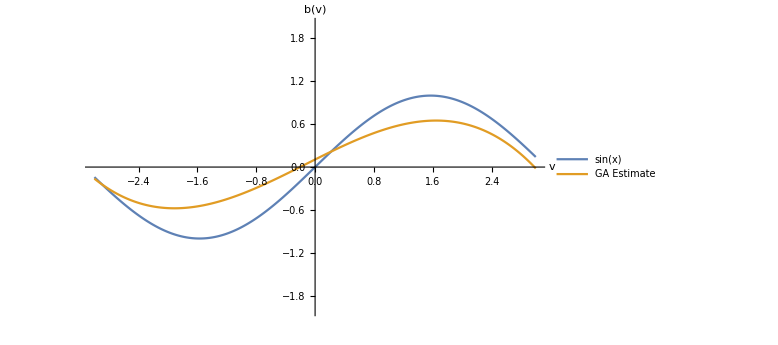
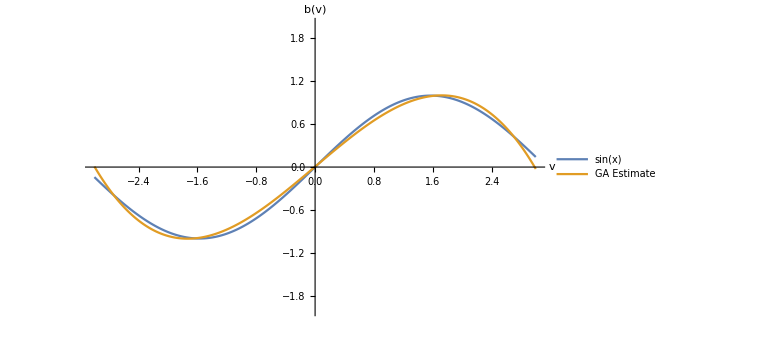

```mathematica
plots=Table[
ListLinePlot[{Transpose[{xs,ysTrue}],Transpose[{xs,ySets[[i]]}]},PlotRange->{-2,2}, AxesLabel->{"v","b(v)"},ImageSize->Large,PlotLegends->Placed[{"sin(x)","GA Estimate"},{Left,Top}], ImageSize->{500,300},AspectRatio->0.6,LabelStyle->14]
,{i,{10,50,100}}
]
```

```mathematica
plots=Table[
ListLinePlot[{Transpose[{xs,ysTrue}],data[[i,1]],data[[i,2]],data[[i,3]]},PlotRange->{0,1}, AxesLabel->{"v","b(v)"},PlotLabel->("Iteration: "<>ToString[i*10]),ImageSize->Large,LabelStyle->12]
,{i,1,100}
];
```

```mathematica
mean=Mean[data[[-100;;]]];
```

```mathematica
d1Mean=D1[xs,mean[[1,All,2]],ysTrue]
d2Mean=D2[xs,mean[[1,All,2]],ysTrue]
```

0.00086556

0.000108623

```mathematica
meanPlot=ListLinePlot[{Transpose[{xs,ysTrue}],mean[[1]],mean[[2]],mean[[3]]},PlotRange->{0,1}, AxesLabel->{"v","b(v)"},PlotLabel->"Mean of final 100 iterations",ImageSize->Large,LabelStyle->12];
```

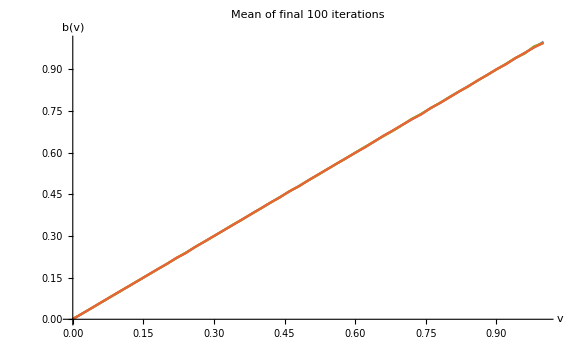

```mathematica
meanPlot
```

```mathematica
fits=-Table[Total[(ysTrue-ySets[[i]])^2],{i,1,100}];
```

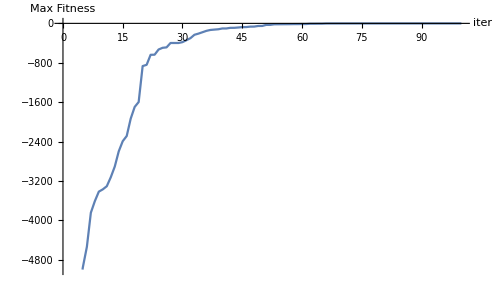

```mathematica
fitfig=ListLinePlot[fits,PlotRange->{-5000,0},AspectRatio->0.6, ImageSize->{500,300},AxesLabel->{"iter","Max Fitness"},LabelStyle->14 ]
```

```mathematica
iters={10,50,100};
```

```mathematica
Do[
Export[NotebookDirectory[]<>"text/chapter_1/figures/sample_sine_"<>ToString[iters[[i]]]<>".jpg",plots[[i]], ImageSize->{500,300},ImageResolution->100];
,{i, 1, 3}
]
```

```mathematica
Export[NotebookDirectory[]<>"text/chapter_1/figures/sample_fit_fig.jpg",fitfig, ImageSize->{500,300},ImageResolution->100];
```

```mathematica
Export[NotebookDirectory[]<>"spa_sym_10_mean.jpg",Column[{meanPlot,Row[{"D1Mean: "<>ToString[d1Mean]," ","D2Mean: "<>ToString[d2Mean]}]}],ImageResolution->100]
```

/home/kajames/Dropbox/Dissertation/spa_sym_10_mean.jpg

```mathematica
Export[NotebookDirectory[]<>"fpa_asym_10_mean.jpg",meanPlot,ImageResolution->100]
```

/home/kajames/Dropbox/Dissertation/fpa_asym_10_mean.jpg

```mathematica
D1[xs_,points_,opt_]:=Module[{res},
res=(points-opt)^2;
(1/(Last[xs]-First[xs]))*Sqrt[Total[(Most[res]+Rest[res])/2 * (Rest[xs]-Most[xs])]]
];
D2[xs_,points_,opt_]:=Module[{res},
res = points-opt;
(1/(Last[xs]-First[xs]))*Total[(Most[res]+Rest[res])/2 * (Rest[xs]-Most[xs])]
]
```

```mathematica
d1s=Table[D1[xs, data[[i,1,All,2]],ysTrue],{i,1,100}];
d2s=Table[D2[xs,  data[[i,1,All,2]],ysTrue],{i,1,100}];
```

```mathematica
d1=Table[D1[xs, ys[[i]],ysTrue],{i,1,100}];
d2=Table[D2[xs,  ys[[i]],ysTrue],{i,1,100}];
```

```mathematica
d1Plots=Table[ListLinePlot[d1[[1;;k]],PlotRange->{{0,100},{0,1}},ImageSize->Small,AxesLabel->{"n","D1"},Mesh->{{k}},LabelStyle->14],{k,{100}}];
d2Plots=Table[ListLinePlot[d2[[1;;k]],PlotRange->{{0,100},{-0.3,0.3}},ImageSize->Small,AxesLabel->{"n","D2"},Mesh->{{k}},LabelStyle->14],{k,{100}}];
```

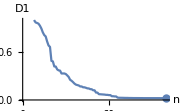

```mathematica
d1Plots[[-1]]
```

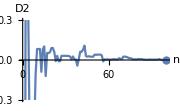

```mathematica
d2Plots[[-1]]
```

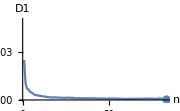

```mathematica
d1Plots[[-1]]
```

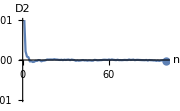

```mathematica
d2Plots[[-1]]
```

```mathematica
Export[NotebookDirectory[]<>"spa_sym_10.gif",Table[Column[{plots[[i]],Row[{d1Plots[[i]],d2Plots[[i]]}]}],{i,1,100}],ImageResolution->100]
```

/home/kajames/Dropbox/Dissertation/spa_sym_10.gif

{-4.46185,0.302305,1.36286,0.225328,-0.701406,-0.551306,-0.550958,-0.550958,-0.107825,0.0821725,0.0825401,0.0825631,-0.0886928,0.0816624,0.102093,-0.120719,0.0524135,0.0524138,0.0588066,0.0896085,0.0899405,0.0595464,-0.00881264,0.0311744,-0.00881804,-0.00881204,0.0311834,0.0311834,0.0311834,0.0311834,0.0311514,0.0299304,0.0262688,0.0043314,0.0265923,0.0040581,0.0043605,-0.0426669,0.00550021,0.0621849,0.0621909,0.0776038,0.107957,0.0294198,0.0249014,0.0286818,0.0248984,0.0246127,0.0247537,0.0402762,0.0386893,0.0402483,0.0402468,0.0411298,0.0353628,-0.0101838,0.00448932,0.00451192,0.00453742,0.00451192,0.00141442,0.00456612,0.00583452,0.00571352,0.00445972,0.00378022,0.0137667,0.00800619,0.00800349,0.0252953,0.0252793,0.0237343,0.0203401,0.0132057,0.0133091,0.0093418,0.00505834,0.00505834,0.00441314,0.00688174,0.00714874,0.00688174,0.00688174,0.00288728,0.00261668,0.00261668,0.000175281,0.00460984,0.00290491,0.00288231,0.00288231,0.00288231,0.00289329,0.00288231,0.00734168,0.00221862,0.000364293,0.000364293,0.000364293,0.000364293}

```mathematica
CDF[NormalDistribution[0.7,0.2],0.1]
```

0.0013499